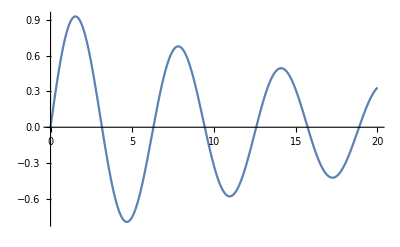

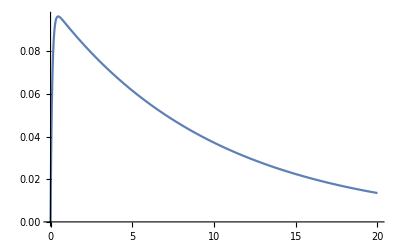

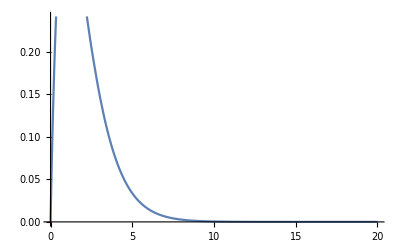

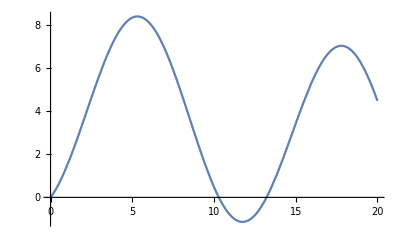

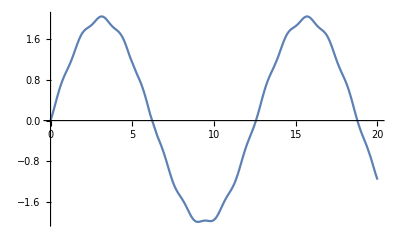

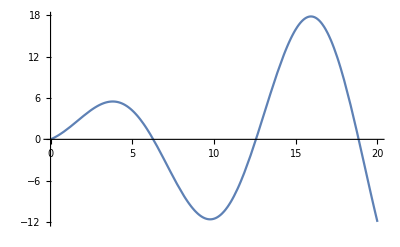

-Graphics3D-

```mathematica
eqdiff[f0_,w0_,gamma_,w_]:={ x''[t] + gamma x'[t] + (w0^2) x[t] == f0 Cos[w t], x'[0]==1 , x[0]==0};

solgen=x[t]/.DSolve[eqdiff[f0,w0,gamma,w],x[t],t];

(*a*)
sola1= x[t]/.DSolve[eqdiff[0,1,(1./10),w],x[t],t];
sola2=x[t]/.DSolve[eqdiff[0,1,10,w],x[t],t];
sola3=x[t]/.DSolve[eqdiff[0,1,2,w],x[t],t];

Plot[sola1,{t,0,20}]
Plot[sola2,{t,0,20}]
Plot[sola3,{t,0,20}]

(*b*)

solb1= x[t]/.DSolve[eqdiff[1,0.5,0,(0.5/10)],x[t],t];
solb2=x[t]/.DSolve[eqdiff[1,0.5,0,5],x[t],t];
solb3=x[t]/.DSolve[eqdiff[1,0.5,0,0.5],x[t],t];

Plot[solb1,{t,0,20}]
Plot[solb2,{t,0,20}]
Plot[solb3,{t,0,20}]

(*c*)

solc=x[t]/.DSolve[eqdiff[3,1,1,w],x[t],t];

Plot3D[solc,{w,0,10},{t,0,100}]
```

```mathematica
(*---------------2-----------------*)
```

```mathematica
A={{-5,-9,8},{9,3,-9},{10,2,7}};
autovett=Eigenvectors[A];
autoval=Eigenvalues[A];
```

```mathematica
(*---------------3-----------------*)
```

```mathematica
polC[lambda_]:=Det[ A-lambda IdentityMatrix[Length[A]]];

radici=x/.Solve[polC[x]==0,x];
```

```mathematica
(*---------------4-----------------*)
```

```mathematica
autovett11={y,z}/.Solve[ (A-(radici[[1]]IdentityMatrix[Length[A]])).{2,y,z}=={0,0,0},{y,z}];

autovett12={y,z}/.Solve[ (A-(radici[[2]]IdentityMatrix[Length[A]])).{2,y,z}=={0,0,0},{y,z}];

autovett13={y,z}/.Solve[ (A-(radici[[3]]IdentityMatrix[Length[A]])).{2,y,z}=={0,0,0},{y,z}];
```

```mathematica
(*---------------5-----------------*)


calcautovett[matr_]:=Module[ {risultato},

n=Length[matr];

polC[lambda_]:=Det[ matr-lambda IdentityMatrix[n]];
rad=x/.Solve[polC[x]==0,x];

For[ j=1, j <n, j++,
risultato[[j]]={y,z}/.NSolve[ (matr-(rad[[j]]IdentityMatrix[n])).{2,y,z}=={0,0,0},{y,z}]
];

risultato
];

M2[n_]:=Table[Random[Real],{n},{n}];
matr=M2[3];

calcautovett[matr]
```

Set::noval: Symbol risultato$6672 in part assignment does not have an immediate value.

risultato$6672

```mathematica
(*---------------6-----------------*)
```

```mathematica
A={{-5,-9,8},{9,3,-9},{10,2,7}};
M= Transpose[A].A;
autoval=Eigenvalues[M];

V=Eigenvectors[M];
S2={{N[autoval[[1]],8],0,0},{0,N[autoval[[2]],8],0},{0,0,N[autoval[[3]],8]}};

base[m_List]:= Table[      
     u[j]= m[[j]]- Sum[ ((m[[j]].u[k-1])/(u[k-1].u[k-1])) u[k-1] , {k, 2, j}];
     u[j]= u[j]/(Sqrt[u[j].u[j]]);
     u[j],
              {j,1,Length[m]}  
                                               ];

matO=base[V];
matS= Sqrt[S2];
matU= A.matO.Inverse[matS];

A===matU.S.Transpose[matO]
```

False

```mathematica
(*---------------7-----------------*)
```